```mathematica
(*电流元的磁场三个分量*)
```

```mathematica
dl=R*ⅆφ*{-Sin[φ],Cos[φ],0};
p={0,y,z};p0={R*Cos[φ],R*Sin[φ],0};
r=√(z^2+y^2+R^2-2R*y*Sin[φ]);
Subscript[e, r]=(p-p0)/r;
(dl×Subscript[e, r])/r^2//Simplify
```

{(R z Cos[φ] ⅆφ)/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),(R z ⅆφ Sin[φ])/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),(R ⅆφ (R-y Sin[φ]))/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2))}

```mathematica
(*Subscript[B, x] 是0*)
```

```mathematica
Integrate[(R z Cos[φ])/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}]
```

ConditionalExpression[0,((R^2+y^2+z^2)/(R y)∉Reals||Re[(R^2+y^2+z^2)/(R y)]≥2||Re[(R^2+y^2+z^2)/(R y)]≤-2)&&(R-y)^2+z^2≠0&&(R+y)^2+z^2≠0]

```mathematica
(*Subscript[B, y],Subscript[B, z] 的分布*)
```

```mathematica
By[y_,z_]:=NIntegrate[(R z Sin[φ])/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}];
Bz[y_,z_]:=NIntegrate[(R(R-y Sin[φ]))/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}];
R=1.0;
Plot[Bz[y,z]/.y->0,{z,-3R,3R},AxesLabel->{"z","Bz"}]
Plot[Bz[y,z]/.z->R/2,{y,-3R,3R},AxesLabel->{"y","Bz"}]
Plot[By[y,z]/.z->R/2,{y,-3R,3R},AxesLabel->{"y","By"}]
Plot3D[Bz[y,z],{y,-3R,3R},{z,-3R,3R},PlotRange->All,PlotPoints->50,Mesh->False,AxesLabel->{"y","z","Bz"}]
```

NIntegrate::inumr: The integrand 1.\ (1.  - y\ Sin[φ])/(« 1 »)^3/2
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

-Graphics-

NIntegrate::inumr: The integrand 1.\ (1.  + 2.99988\ Sin[φ])/(9.99926  + « 1 » + « 18 »\ « 1 »)^3/2
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

-Graphics-

NIntegrate::inumr: The integrand 1.\ z\ Sin[φ]/(9.99926  + « 1 » + « 18 »\ « 1 »)^3/2
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

-Graphics-

-Graphics3D-

```mathematica
(*磁力线的折线法*)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {4.65093}. NIntegrate obtained -4.11997×10^-18 and 5.35155×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {1.30072}. NIntegrate obtained 4.3097×10^-18 and 8.14538×10^-18 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {0.0000241858}. NIntegrate obtained 1.63986×10^-18 and 2.39226×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate :: ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: slwcon will be suppressed during this calculation.

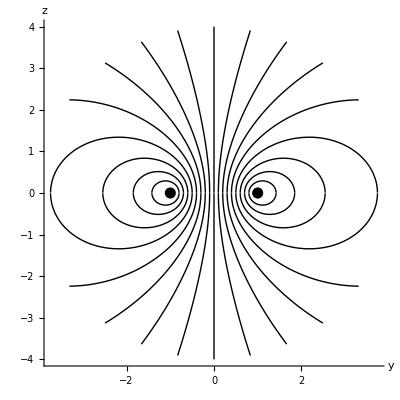

```mathematica
By[y_,z_]:=NIntegrate[(R z Sin[φ])/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}];
Bz[y_,z_]:=NIntegrate[(R(R-y Sin[φ]))/((R^2+y^2+z^2-2 R y Sin[φ])^(3/2)),{φ,0,2π}];
R=1.0;r1=step=0.005R;r2=4R;forceline={};
Do[θ=π/2.0;p={y0,r1};single={};
While[(Abs[p[[2]]]≥r1)∧(Norm[p]<r2),
AppendTo[single,p];p=p+step*{Cos[θ],Sin[θ]};
θ=Arg[By[p[[1]],p[[2]]]+ⅈ*Bz[p[[1]],p[[2]]]]];
AppendTo[forceline,single];m=Length[single];
single=Table[{single[[j,1]],-single[[j,2]]},{j,m}];
AppendTo[forceline,single],{y0,-8R/10,8R/10,R/10}]
Show[Graphics[{Line/@forceline}],Axes->True,AxesLabel->{"y","z"},AspectRatio->1,Epilog->{PointSize[0.02],Point/@{{R,0},{-R,0}}}]
```

```mathematica
Clear[By,Bz,R,r1,r2,step,forceline,θ,p,single,m]
```